# Animiranje grafov, vektorji in matrike

## Animiranje grafov

### Subsection. naloga:

Narišite graf funkcije y=a sin (k x+n) tako, da boste lahko vrednosti parametrov a, k in n spreminjali v obsegu od -3 do 3. Območje risanja omejite na [-5,5]×[-5,5]. Enoti na x in y osi naj bosta enako veliki.

```mathematica
(* V funkciji Plot uporabite nastavitvi PlotRange->{-5,5} in AspectRatio->Automatic *)
```

```mathematica
f[x_,a_,k_,n_]:=a Sin[(k x)+n]
Manipulate[
Plot[f[x,a,k,n],{x,-5,5},PlotRange->{-5,5},AspectRatio->Automatic],{a,-3,3},{k,-3,3},{n,-3,3}
]
```

### Subsection. naloga:

Narišite graf premice y=k x+n  in na isti sliki še pravokotnico nanjo, ki gre skozi točko T(x_0,y_0) tako, da boste lahko spreminjali vrednosti parametrov k, n, x_0 in y_0. Na sliki označite z majhnim krogcem, kje leži točka T.
Namig: dva grafa na isti sliki narišete s funkcijo Plot tako, da predpisa podate v seznamu: {f[x], g[x]}.

```mathematica
(* Točko dodate z nastavitvijo Epilog->{PointSize[Large],Point[{{x0,y0}}]}] *)
```

```mathematica
ClearAll
```

ClearAll

```mathematica
f[x_,k_,n_]:=(k x)+n
g[x_,k_,x0_,y0_]:=((-(1/k)) x)+y0+((1/k) x0)
Point[{x0,y0}]
```

Point[{x0,y0}]

Point[{x0,y0}]

```mathematica
Manipulate[
Plot[{f[x,k,n],g[x,k,x0,y0]},{x,-10,10},PlotRange->{-5,5},AspectRatio->Automatic,Epilog->{PointSize[Large],Point[{{x0,y0}}]}],{k,-5,5},{n,-5,5},{x0,-5,5},{y0,-5,5}
]
```

### Subsection. naloga:

Definirajte funkcijo  f(x)=(x(x-2))^2/(x^2+1) ter narišite njen graf skupaj s tangento v točki x_0, tako da boste lahko spreminjali vrednosti parametra x_0. Na sliki označite z majhnim krogcem, kje se tangenta dotika grafa funkcije.

```mathematica
ClearAll
```

ClearAll

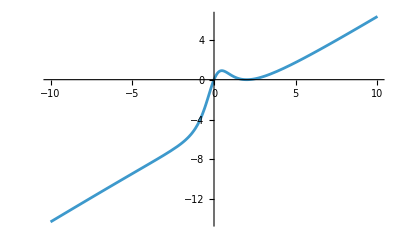

```mathematica
f[x_]:=(x ((x-2)^2))/((x^2)+1)
Plot[f[x],{x,-10,10}]
```

```mathematica
g[x_,x0_]:=((f'[x0]) x)+f[x0]-((f'[x0]) x0)
Point[{x0,y0}]
```

Point[{x0,y0}]

```mathematica
Manipulate[
Plot[{f[x],g[x,x0]},{x,-10,10},PlotRange->{-5,5},AspectRatio->Automatic,Epilog->{PointSize[Large],Point[{{x0,f[x0]}}]}],{x0,-5,5}]
```

### Subsection. naloga:

1. Narišite graf implicitno podane funkcije  |x|^(2/3)+|y|^(2/3)=1  na območju [-1,1]×[-1,1]
2. Prikažite, kako se spreminja graf implicitne krivulje  |x|^p+|y|^p=1  za vrednosti parametra p∈[0,4]  z začetno vrednostjo 2.
3. Pri kateri vrednosti p leži točka (1/3,1/3) na grafu krivulje?

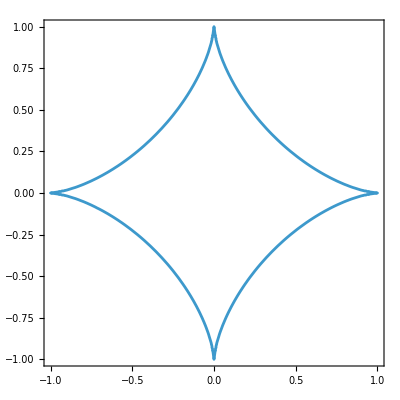

```mathematica
ContourPlot[((Abs[x])^(2/3))+((Abs[y])^(2/3))==1,{x,-1,1},{y,-1,1}]
```

```mathematica
Manipulate[
ContourPlot[((Abs[x])^(p))+((Abs[y])^(p))==1,{x,-1,1},{y,-1,1}],{{p,2},0,4}]
```

## Vektorji in matrike

```mathematica
ClearAll
```

ClearAll

### Subsection. naloga:

1. Dana sta vektorja  (v⃗)_1=(1,2,3)  in  (v⃗)_2=(-3,-2,5). Zapiši ju kot dve spremenljivki.
2. Izračunaj njun skalarni produkt.
3. Izračunaj njun vektorski produkt.s
4. Kateri od vektorjev je daljši?
5. Sestavi enačbo ravnine, ki gre skozi točko (1,1,1) in ima normalo v smeri vektorskega produkta.

```mathematica
Element[v1,Vectors]
Element[v2,Vectors]
v1={1,2,3}
v2={-3,-2,5}
```

{1,2,3}∈Vectors

{-3,-2,5}∈Vectors

{1,2,3}

{-3,-2,5}

```mathematica
Dot[v1,v2]
```

8

```mathematica
Cross[v1,v2]
```

{16,-14,4}

```mathematica
Sqrt[(1^2)+(2^2)+(3^2)]
```

√14

```mathematica
Norm[v1]
```

√14

```mathematica
Norm[v2]
```

√38

```mathematica
Max[Norm[v1],Norm[v2]]
```

√38

```mathematica
16x-14y+4z==6
```

16 x-14 y+4 z==6

### Subsection. naloga:

Naj bodo a⃗, b⃗ in c⃗ vektorji v R^3. S simboličnim računom dokaži identiteto  a⃗×(b⃗×c⃗)=(a⃗·c⃗)b⃗-(a⃗·b⃗)c⃗

```mathematica
ClearAll
```

ClearAll

```mathematica
Element[a,Vectors]
Element[b,Vectors]
Element[c,Vectors]

a={a1,a2,a3}
b={b1,b2,b3}
c={c1,c2,c3}
```

{a1,a2,a3}∈Vectors

{b1,b2,b3}∈Vectors

c∈Vectors

{a1,a2,a3}

{b1,b2,b3}

{c1,c2,c3}

```mathematica
Reduce[Cross[a,Cross[b,c]]==(Dot[Dot[a,c],b]-Dot[Dot[a,b],c])]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{-a2 b2 c1-a3 b3 c1+a2 b1 c2+a3 b1 c3,a1 b2 c1-a1 b1 c2-a3 b3 c2+a3 b2 c3,a1 b3 c1+a2 b3 c2-a1 b1 c3-a2 b2 c3}==-(a1 b1+a2 b2+a3 b3).{c1,c2,c3}+(a1 c1+a2 c2+a3 c3).{b1,b2,b3}]

```mathematica
Simplify[Cross[a,Cross[b,c]]-(Dot[a,c] b-Dot[a,b] c)]
```

{0,0,0}

### Subsection. naloga:

Dokaži, da za poljubni 2×2 matriki A in B velja enakost  (A B)^-1=B^-1 A^-1.

```mathematica
ClearAll[a,b,c,f,g]
```

```mathematica
A={{a,b},{c,d}}
B={{e,f},{g,h}}
```

{{a,b},{c,d}}

{{e,f},{g,h}}

```mathematica
Inverse[A B]=Inverse[B] Inverse[A]
```

Set::write: Tag Inverse in { is Protected.

{{(d h)/((-b c+a d) (-f g+e h)),(b f)/((-b c+a d) (-f g+e h))},{(c g)/((-b c+a d) (-f g+e h)),(a e)/((-b c+a d) (-f g+e h))}}

```mathematica
Simplify[((A B)^(-1))-((B^(-1)) (A^(-1)))]
```

{{0,0},{0,0}}

### Subsection. naloga:

1. Dana je matrika  M=(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1).  Zapiši jo kot spremenljivko.
2. Izračunaj njeno determinanto.
3. Izračunaj njene lastne vrednosti.
4. Izračunaj njene lastne vektorje.
5. Ali je matrika diagonalizabilna?
6. Matriko želimo diagonalizirati. Konstruiraj diagonalno matriko (po diagonali ima lastne vrednosti), prehodno matriko (za stolpce ima lastne vektorje) in inverz prehodne matrike.
7. Preveri, ali velja pogoj za diagonalizabilnost.

```mathematica
ClearAll
```

```mathematica
ClearAll
ClearAll[a,b,c]
Clear[P , Č, F, K]
```

ClearAll

```mathematica
M={{9,2,-3},{3,2,1},{6,4,-1}}
```

{{9,2,-3},{3,2,1},{6,4,-1}}

```mathematica
Det[M]
```

-36

```mathematica
L=Eigenvalues[M]
```

{3 (1+√2),4,3 (1-√2)}

```mathematica
KKKK=Eigenvectors[M]
```

{{-(-6-5 √2)/(6 (1+√2)),-(-2-√2)/(2 (1+√2)),1},{2,7,8},{-(-5+3 √2)/(3 √2 (-1+√2)),-(2-√2)/(2 (-1+√2)),1}}

```mathematica
DiagonalizableMatrixQ[M]
```

True

```mathematica
o=DiagonalMatrix[L]
```

{{3 (1+√2),0,0},{0,4,0},{0,0,3 (1-√2)}}

```mathematica
P=Transpose[KKKK]
```

{{-(-6-5 √2)/(6 (1+√2)),2,-(-5+3 √2)/(3 √2 (-1+√2))},{-(-2-√2)/(2 (1+√2)),7,-(2-√2)/(2 (-1+√2))},{1,8,1}}

```mathematica
F=Inverse[P];
```

```mathematica
Simplify[P.o.F]
```

{{9,2,-3},{3,2,1},{6,4,-1}}

{{(3 (1-√2) (5/(-1+√2)-29/(3 √2 (-1+√2))))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))-((-6-5 √2) (7+8/(-1+√2)-(4 √2)/(-1+√2)))/(2 (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))-(2 (-2-√2) (-2-8/(-1+√2)+(20 √2)/(3 (-1+√2))))/((1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))),(24 (1-√2) (5/(-1+√2)-29/(3 √2 (-1+√2))))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))+(6 (1+√2) (7+8/(-1+√2)-(4 √2)/(-1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))+(28 (-2-8/(-1+√2)+(20 √2)/(3 (-1+√2))))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(3 (1-√2) (5/(-1+√2)-29/(3 √2 (-1+√2))))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))-((1+√2) (-5+3 √2) (7+8/(-1+√2)-(4 √2)/(-1+√2)))/(√2 (-1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))-(2 (2-√2) (-2-8/(-1+√2)+(20 √2)/(3 (-1+√2))))/((-1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))},{(2 √2 (1-√2))/((-1+√2) (1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))-((-6-5 √2) (-1/(-1+√2)+1/(√2 (-1+√2))-1/(1+√2)-1/(√2 (1+√2))))/(2 (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))-(2 (-2-√2) (1/(-1+√2)-5/(3 √2 (-1+√2))+1/(1+√2)+5/(3 √2 (1+√2))))/((1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))),(16 √2 (1-√2))/((-1+√2) (1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))+(6 (1+√2) (-1/(-1+√2)+1/(√2 (-1+√2))-1/(1+√2)-1/(√2 (1+√2))))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))+(28 (1/(-1+√2)-5/(3 √2 (-1+√2))+1/(1+√2)+5/(3 √2 (1+√2))))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(2 √2 (1-√2))/((-1+√2) (1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))-((1+√2) (-5+3 √2) (-1/(-1+√2)+1/(√2 (-1+√2))-1/(1+√2)-1/(√2 (1+√2))))/(√2 (-1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))-(2 (2-√2) (1/(-1+√2)-5/(3 √2 (-1+√2))+1/(1+√2)+5/(3 √2 (1+√2))))/((-1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))},{(3 (1-√2) (5/(1+√2)+29/(3 √2 (1+√2))))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))-(2 (-2-√2) (2-8/(1+√2)-(20 √2)/(3 (1+√2))))/((1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))-((-6-5 √2) (-7+8/(1+√2)+(4 √2)/(1+√2)))/(2 (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))),(24 (1-√2) (5/(1+√2)+29/(3 √2 (1+√2))))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))+(28 (2-8/(1+√2)-(20 √2)/(3 (1+√2))))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))+(6 (1+√2) (-7+8/(1+√2)+(4 √2)/(1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(3 (1-√2) (5/(1+√2)+29/(3 √2 (1+√2))))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))-(2 (2-√2) (2-8/(1+√2)-(20 √2)/(3 (1+√2))))/((-1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))-((1+√2) (-5+3 √2) (-7+8/(1+√2)+(4 √2)/(1+√2)))/(√2 (-1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))}}